## Differences between primes

```mathematica
result={};n=5;primes=allPrimes[[n]];
```

## Prime-5

```mathematica
diffs = Table[primes[[n+1]]-primes[[n]],{n,Length@primes-1}];
```

## Visibility Graph

```mathematica
visibles={};Do[
Do[
If[visibleQ[i,j,diffs],AppendTo[visibles,i->j],Null],
{j,i+1,Length@diffs}
],
{i,1,Length@diffs-1}];
```

## Graph

```mathematica
g5=Graph[visibles[[;;100]], DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];gv5=Overlay[{g5,Style["d=5", FontFamily->"Times"]}, Alignment->Center, ImageSize->Large];
```

```mathematica
igv5=Graph[visibles, VertexLabels->"Name",DirectedEdges->False,VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
count = Total[AdjacencyMatrix[igv5]]//Counts
```

<|47→4,48→3,49→5,50→2,42→2,51→1,55→1,59→2,53→3,62→1,69→1,70→1,63→1,64→1,72→1,71→1,91→2,92→1,86→1,118→1,111→1,127→2,80→1,167→1,28→4,152→1,33→4,162→1,153→1,177→1,210→1,187→1,206→1,45→1,43→1,39→2,35→1,32→1,30→2,31→2,24→2,27→4,20→4,23→5,29→2,18→8,21→8,16→8,26→2,15→8,22→4,17→8,13→13,14→10,12→15,10→14,11→8,19→4,3→63,9→14,25→1,8→23,2→45,5→37,7→33,4→60,6→31,1→1|>

```mathematica
Sort[count]
```

<|51→1,55→1,62→1,69→1,70→1,63→1,64→1,72→1,71→1,92→1,86→1,118→1,111→1,80→1,167→1,152→1,162→1,153→1,177→1,210→1,187→1,206→1,45→1,43→1,35→1,32→1,25→1,1→1,50→2,42→2,59→2,91→2,127→2,39→2,30→2,31→2,24→2,29→2,26→2,48→3,53→3,47→4,28→4,33→4,27→4,20→4,22→4,19→4,49→5,23→5,18→8,21→8,16→8,15→8,17→8,11→8,14→10,13→13,10→14,9→14,12→15,8→23,6→31,7→33,5→37,2→45,4→60,3→63|>

```mathematica
countrel = Table[{x,count[x]/Length@diffs}, {x,Keys[count]}][[;;-2]]
```

{{47,1/125},{48,3/500},{49,1/100},{50,1/250},{42,1/250},{51,1/500},{55,1/500},{59,1/250},{53,3/500},{62,1/500},{69,1/500},{70,1/500},{63,1/500},{64,1/500},{72,1/500},{71,1/500},{91,1/250},{92,1/500},{86,1/500},{118,1/500},{111,1/500},{127,1/250},{80,1/500},{167,1/500},{28,1/125},{152,1/500},{33,1/125},{162,1/500},{153,1/500},{177,1/500},{210,1/500},{187,1/500},{206,1/500},{45,1/500},{43,1/500},{39,1/250},{35,1/500},{32,1/500},{30,1/250},{31,1/250},{24,1/250},{27,1/125},{20,1/125},{23,1/100},{29,1/250},{18,2/125},{21,2/125},{16,2/125},{26,1/250},{15,2/125},{22,1/125},{17,2/125},{13,13/500},{14,1/50},{12,3/100},{10,7/250},{11,2/125},{19,1/125},{3,63/500},{9,7/250},{25,1/500},{8,23/500},{2,9/100},{5,37/500},{7,33/500},{4,3/25},{6,31/500}}

```mathematica
countrel={{47,1/125},{48,3/500},{49,1/100},{50,1/250},{42,1/250},{51,1/500},{55,1/500},{59,1/250},{53,3/500},{62,1/500},{69,1/500},{70,1/500},{63,1/500},{64,1/500},{72,1/500},{71,1/500},{91,1/250},{92,1/500},{86,1/500},{118,1/500},{111,1/500},{127,1/250},{80,1/500},{167,1/500},{28,1/125},{152,1/500},{33,1/125},{162,1/500},{153,1/500},{177,1/500},{210,1/500},{187,1/500},{206,1/500},{45,1/500},{43,1/500},{39,1/250},{35,1/500},{32,1/500},{30,1/250},{31,1/250},{24,1/250},{27,1/125},{20,1/125},{23,1/100},{29,1/250},{18,2/125},{21,2/125},{16,2/125},{26,1/250},{15,2/125},{22,1/125},{17,2/125},{13,13/500},{14,1/50},{12,3/100},{10,7/250},{11,2/125},{19,1/125},{3,63/500},{9,7/250},{25,1/500},{8,23/500},{2,9/100},{5,37/500},{7,33/500},{4,3/25},{6,31/500}};
```

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[0.258773/x^0.918865]

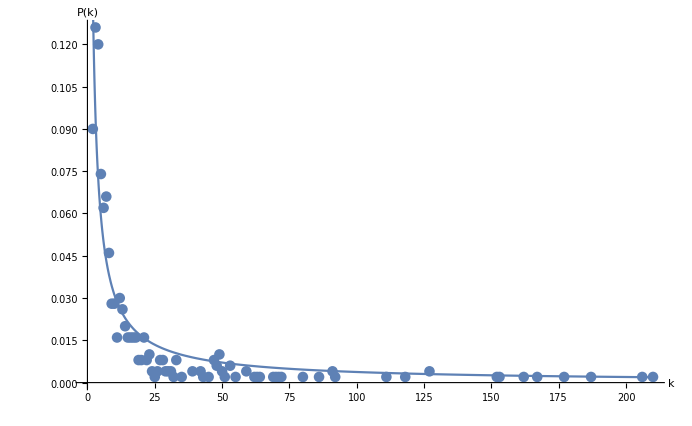

```mathematica
vis5=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[countrel[[All,1]]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large, ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"v-5.eps",vis5];
```

## Mean degree

```mathematica
degree=VertexDegree[igv5]//Mean//N
```

16.092

## Record result

```mathematica
AppendTo[result,Flatten[{"visibility", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Horizontal Visibility Graph

```mathematica
horizontals={};Do[
Do[
If[horizontalQ[i,j,diffs],AppendTo[horizontals,i->j],Null],
{j,i+1,Length@diffs}
],
{i,1,Length@diffs-1}];
```

## Graph

```mathematica
h5=Graph[horizontals[[;;100]], DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];gh5=Overlay[{h5,Style["d=5", FontFamily->"Times"]}, Alignment->Center, ImageSize->Large];
```

```mathematica
igh5=Graph[horizontals, VertexLabels->"Name",VertexLabelStyle->Large,DirectedEdges->False,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igh5];
```

```mathematica
count = Total[adj]//Counts
```

<|1→2,2→174,3→106,4→84,5→50,8→14,7→13,6→37,9→11,10→4,11→3,13→1,14→1|>

```mathematica
Sort[count]
```

<|13→1,14→1,1→2,11→3,10→4,9→11,7→13,8→14,6→37,5→50,4→84,3→106,2→174|>

```mathematica
countrel = Table[{x,count[x]/Length@diffs}, {x,Keys[count]}][[2;;]]
```

```mathematica
countrel={{2,87/250},{3,53/250},{4,21/125},{5,1/10},{8,7/250},{7,13/500},{6,37/500},{9,11/500},{10,1/125},{11,3/500},{13,1/500},{14,1/500}}
```

{{2,87/250},{3,53/250},{4,21/125},{5,1/10},{8,7/250},{7,13/500},{6,37/500},{9,11/500},{10,1/125},{11,3/500},{13,1/500},{14,1/500}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[1.0632/x^1.54544]

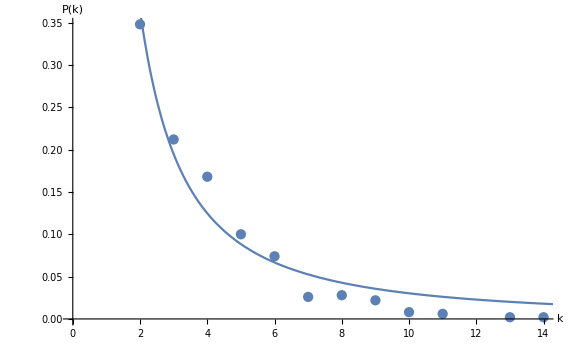

```mathematica
hvis5=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large, ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"hv-5.eps",hvis5];
```

## Mean degree

```mathematica
degree=VertexDegree[igh5]//Mean//N;
```

## Record result

```mathematica
AppendTo[result,Flatten[{"horizontal", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Return result

```mathematica
result
```

{{visibility,5,500,16.092,0.918865 ± 0.115679,0.258773 ± 0.0499296},{horizontal,5,500,3.756,1.54544 ± 0.288127,1.0632 ± 0.310422}}